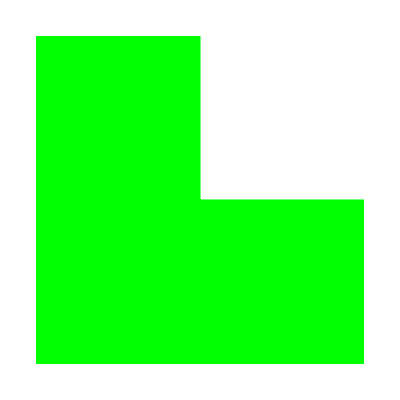

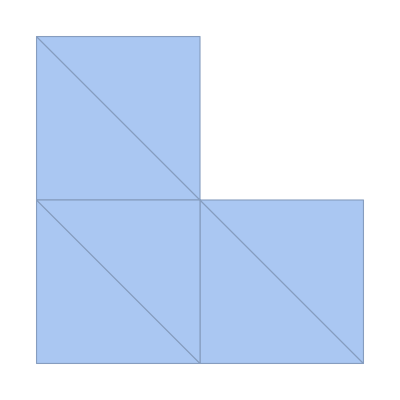

1

-Graphics3D-

-Graphics3D-

```mathematica
P={
{0,0},
{1,0},
{2,0},
{0,1},
{1,1},
{2,1},
{0,2},
{1,2}
};
T={
{1,2,4},
{2,5,4},
{2,3,5},
{3,6,5},
{4,5,7},
{5,8,7}
};
constructElements[nodes_,nodeIndexArr_]:=Polygon[Table[nodes⟦#⟦k⟧⟧,{k,1,Length[#]}]]&/@nodeIndexArr
triangleTable =constructElements[P,T];
Graphics[{EdgeForm[Directive[Dashed]],Green,triangleTable}]
meshReg=MeshRegion[P,Polygon/@T]

inRegion[regions_,coordinates_]:=Module[{ind=1,len=Length[regions]},
While[!(coordinates∈regions⟦ind⟧),
++ind;
If[ind>len,ind=0;Break[]];
];
ind
]
inRegion[triangleTable, {1,0}]
(*inRegion[meshReg, {1,0}]*)

hatFunctions[k_,nodes_?ListQ,nodeIndexArr_?ListQ,elements_?ListQ,coordinates_]:=Module[{elIndex=inRegion[elements,coordinates],dims=Length[nodes⟦1⟧]},
(*If it is not part of the region of elements, return 0*)
If[elIndex==0, Return[0]];
nodesForElement = nodeIndexArr⟦elIndex⟧;
(*Take which index in vector equation must have non-zero in RHS*)
indexInPolygon=FirstPosition[nodesForElement,k];
If[MissingQ[indexInPolygon], Return[0]];
rhs=Table[0,dims+1];
rhs⟦indexInPolygon⟧=1;
lhs=Table[Append[nodes⟦nodesForElement⟦j⟧⟧,1],{j,1,dims+1}];
coeffs = LinearSolve[lhs,rhs];
Return[Sum[coeffs⟦j⟧coordinates⟦j⟧,{j,1,dims}]+coeffs⟦dims+1⟧]
]

Plot3D[hatFunctions[5,P,T,triangleTable,{x,y}],{x,y} ∈ meshReg,PlotPoints->10]

phi[coordinates_?ListQ]:=coordinates⟦1⟧^2+coordinates⟦2⟧^2
nodeInterpolate[nodes_?ListQ,nodeIndexArr_?ListQ,elements_?ListQ,f_,coordinates_]:=Sum[f[nodes⟦k⟧] hatFunctions[k,nodes,nodeIndexArr,elements,coordinates],{k,1,Length[nodes]}]
Plot3D[nodeInterpolate[P,T,triangleTable,phi,{x,y}],{x,y} ∈ meshReg,PlotPoints->10]
```

```mathematica
(*triangleTable = Function[element,
Triangle[Table[P⟦element⟦k⟧⟧,{k,1,Length[element]}]]
]/@T;
Position[triangleTable, RegionMember[_,{1,1}]]
Position[triangleTable, {0.5,0.5}∈_]*)
```

```mathematica
Plot3D[phi[{x,y}],{x,y} ∈ meshReg,PlotPoints->10]
```

-Graphics3D-